Dynamic and Graphic commands

```mathematica
pet=RandomChoice[{"cat","bird","pig","dog","goat","fish"},50];
status=RandomChoice[{"healthy","sick"},50]
loc=RandomReal[{0,1},{50,2}];
dat={pet,loc,status}// Transpose
```

{sick,sick,healthy,sick,healthy,sick,sick,sick,healthy,sick,healthy,healthy,sick,sick,sick,sick,sick,healthy,sick,healthy,healthy,healthy,healthy,sick,sick,sick,sick,sick,healthy,sick,sick,sick,healthy,healthy,sick,sick,healthy,healthy,healthy,healthy,sick,healthy,healthy,healthy,sick,healthy,healthy,sick,healthy,sick}

{{pig,{0.846601,0.951023},sick},{fish,{0.650687,0.942593},sick},{goat,{0.423799,0.363299},healthy},{goat,{0.726864,0.823876},sick},{fish,{0.740654,0.971778},healthy},{bird,{0.37893,0.547932},sick},{goat,{0.348801,0.0117064},sick},{cat,{0.815475,0.525588},sick},{cat,{0.475756,0.0234055},healthy},{goat,{0.340257,0.0748458},sick},{pig,{0.767941,0.789988},healthy},{goat,{0.967121,0.397961},healthy},{pig,{0.427085,0.816595},sick},{cat,{0.572807,0.504794},sick},{fish,{0.545307,0.337032},sick},{dog,{0.0971625,0.0895695},sick},{fish,{0.954195,0.322534},sick},{fish,{0.840873,0.843932},healthy},{goat,{0.863265,0.52055},sick},{goat,{0.718844,0.970361},healthy},{pig,{0.126048,0.902601},healthy},{pig,{0.2579,0.823609},healthy},{pig,{0.896573,0.503589},healthy},{fish,{0.458909,0.211839},sick},{bird,{0.244415,0.705627},sick},{goat,{0.95212,0.256456},sick},{cat,{0.362174,0.934565},sick},{fish,{0.896115,0.755036},sick},{bird,{0.537494,0.4615},healthy},{cat,{0.0867087,0.433771},sick},{cat,{0.571798,0.346139},sick},{goat,{0.631656,0.618598},sick},{pig,{0.559694,0.428138},healthy},{fish,{0.0382798,0.482737},healthy},{goat,{0.197525,0.675873},sick},{bird,{0.13651,0.989524},sick},{fish,{0.627373,0.740151},healthy},{pig,{0.64363,0.496707},healthy},{fish,{0.487598,0.69718},healthy},{dog,{0.673277,0.664103},healthy},{bird,{0.892416,0.717787},sick},{dog,{0.777865,0.316825},healthy},{cat,{0.857893,0.523525},healthy},{cat,{0.657767,0.335475},healthy},{cat,{0.716405,0.433768},sick},{pig,{0.339978,0.414086},healthy},{fish,{0.799892,0.494887},healthy},{cat,{0.405925,0.673532},sick},{cat,{0.425755,0.608051},healthy},{pig,{0.327984,0.0897},sick}}

```mathematica
(*Create an equilaterial triangle from x and y, Scaled by s*)
f[{x_,y_},s_]:=Polygon[
{s*Cos[Pi/2]+x,s*Sin[Pi/2]+y},
{s*Cos[Pi/6]+x,s*Sin[Pi/6]+y},
{s*Cos[7*Pi/6]+x,s*Sin[7*Pi/6]+y}
]

equiTri[{x_,y_},s_]:=Polygon[Table[{s*Cos[i]+x,s*Sin[i]+y},{i,-Pi/6,7Pi/6,2Pi/3}]]
```

```mathematica
(*Highlight the dogs*)
marker[x_]:=If[x[[1]]=="dog",equiTri[x[[2]],.01],Point[x[[2]]]]

(*Creates a list where you have a color and a point*)
pointfn[x_]:={If[x[[3]]=="healthy",Green,Red],marker[x]}
```

```mathematica
(*Apply point function to everything in the list*)
pointfn[#]& /@ dat //Graphics
```

-Graphics-

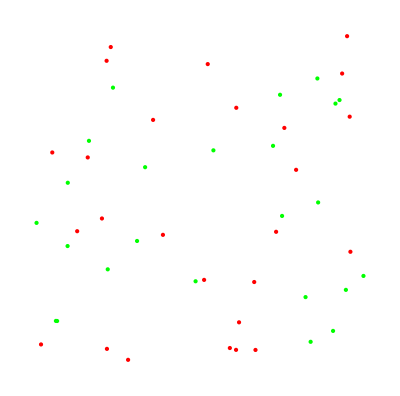

```mathematica
Flatten[pointfn[#]& /@ dat]// Graphics
```

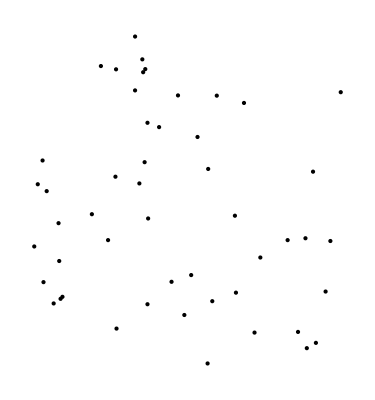

```mathematica
Point[dat[[All,2]]]//Graphics
```

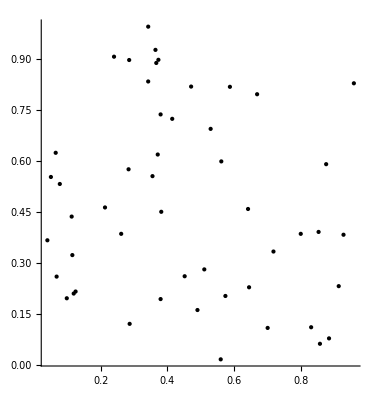

```mathematica
Graphics[Point[dat[[All,2]]],Axes->True]
```

{RGBColor[1,0,0],Point[{{0.379667,0.193365},{0.364247,0.92602},{0.379668,0.736242},{0.240079,0.905979},{0.366707,0.887533},{0.0680283,0.25946},{0.927829,0.382525},{0.285473,0.896197},{0.050867,0.552352},{0.857208,0.0619261},{0.913496,0.231354},{0.490138,0.161171},{0.700489,0.108553},{0.373063,0.896836},{0.283645,0.574934},{0.113118,0.435909},{0.45177,0.26049},{0.958892,0.827773},{0.0403306,0.36619},{0.0775932,0.531755},{0.830827,0.110535},{0.286886,0.120532},{0.471104,0.818134},{0.342524,0.994288},{0.115144,0.322675}}],RGBColor[0,0,1],Point[{{0.119211,0.2096},{0.587379,0.817409},{0.414483,0.723292},{0.355354,0.554794},{0.37108,0.618368},{0.213035,0.462728},{0.342447,0.833111},{0.717919,0.333157},{0.644804,0.228015},{0.64171,0.458229},{0.381624,0.449977},{0.56158,0.598113},{0.529629,0.693772},{0.799699,0.385173},{0.559828,0.0161643},{0.124855,0.215572},{0.573872,0.20249},{0.261528,0.385195},{0.0652517,0.623442},{0.88445,0.0778058},{0.875829,0.589976},{0.0984885,0.195735},{0.510628,0.280615},{0.853131,0.390777},{0.668896,0.795594}}]}

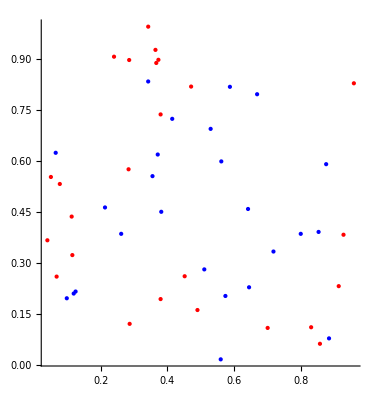

```mathematica
{Red,Point[dat[[1;;25,2]]],Blue,Point[dat[[26;;,2]]]}
Graphics[%,Axes->True]
```